```mathematica
Quit[]
```

## Load Model and Compute Diagrams

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
$FCVerbose=0;
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$FAVerbose=0;
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;

(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-SMQCD-NLO_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
```

## g-g- t- t (self energy)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →4, with {} →{-F[9],F[9],V[4],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3,p4}).
However the choice below produces nicer diagrams.

```mathematica
topsCT = CreateCTTopologies[1,2->2,ExcludeTopologies->{WFCorrectionCTs,TadpoleCTs,BoxCTs,TriangleCTs}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGT = { V[1],V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[Join[topsCT,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1]}];
```

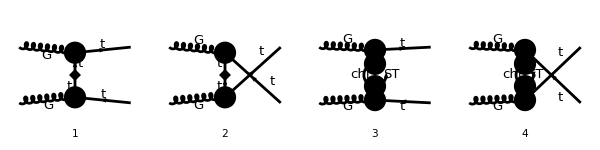

```mathematica
goodDiags=DiagramExtract[allDiags,{1,2,10,11}];
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 600,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

## Compute Amplitude

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{-p4,-p3},LorentzIndexNames->{ν,μ},OutgoingMomenta->{p2,p1},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,FR$deltaZ[{G,G},{{}}]->deltaZG,FR$deltaZ[{t,t},{{}},"L"]->deltaZL,FR$deltaZ[{t,t},{{}},"R"]->deltaZR,FR$delta[{MT},{}]->deltaM,FR$delta[{aS},{}]->deltaaS};
(* Replace the momenta to simplify the results *)
ampA1=FCReplaceMomenta[ampA,{p2->p23-p3,p1->p13-p3}];
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA1]]];
```

```mathematica
CTsubs={deltaZG->0,deltaaS->0,deltaZL -> Pi^2yDM^2  MT^2  Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]],deltaZR-> Pi^2  yDM^2( MT^2 Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]]+PaVe[1,{MT^2},{mChi^2,mST^2},PaVeAutoOrder->False,PaVeAutoReduce->False]),deltaM->-Pi^2/2 yDM^2 MT PaVe[1,{MT^2},{mChi^2,mST^2},PaVeAutoOrder->False,PaVeAutoReduce->False]};
ampB2=ampB/.CTsubs;
```

Evaluate Loop integrals:

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[Expand[ampB2],q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True,PaVeAutoOrder->False]//Simplify),LorentzIndexNames-> {μ,ν}];
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

```mathematica
(* Simplify Loop expressions *)
ampEsimp2a=FullSimplify[DiracSimplify[ampEsimp/.{B0[a_,m1_,m2_]->1/(a+m1-m2)(A0[m1]-A0[m2]-2 a PaVe[1,{a},{m1,m2},PaVeAutoOrder->False,PaVeAutoReduce->False])}]];
```

```mathematica
(* Restore momenta *)
(* ampEsimp2=FullSimplify[ExpandScalarProduct[FCReplaceMomenta[ampEsimp2a,{p23->p2+p3,p13->p1+p3}]]];*)
ampEsimp2=ampEsimp2a;
```

## Check Divergences (note that the DB1 loop integral is finite)

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsUV=Table[lInt->PaXEvaluateUV[lInt,PaXImplicitPrefactor->1/(2 Pi)^4],{lInt,lInts}];
lIntsUV//MatrixForm
```

PaXEvaluate::convFail: Warning! Not all scalar loop integrals in the expression could be prepared to be processed with Package X. Following integrals will not be handled by Package X: {DB1(MT^2,mChi^2,mST^2,BReduce→False)}

(DB1(MT^2,mChi^2,mST^2,BReduce→False)→0
B_1(MT^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
B_1(p13^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
B_1(p23^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV))

```mathematica
loopUV=FullSimplify[ampEsimp2/.lIntsUV]
```

0

## Simplify Result

```mathematica
ampEsimp3a=Simplify[DiracSimplify[FeynAmpDenominatorExplicit[ampEsimp2]]];
```

### Order PaVe integrals

```mathematica
lInts = Cases2[ampEsimp3a,{A0,B0,C0,B1,D0,PaVe}];
orderedPaVes=Table[lInt->PaVeOrder[lInt,PaVeOrderList->{mChi^2,mST^2},Sum->True],{lInt,lInts}];
ampEsimp4=ampEsimp3a/.orderedPaVes;
lIntsOrdered = Cases2[ampEsimp4,{A0,B0,C0,D0,B1,PaVe}];
lIntsOrdered//MatrixForm
```

(B_1(MT^2,mChi^2,mST^2)
B_1(p13^2,mChi^2,mST^2)
B_1(p23^2,mChi^2,mST^2))

### Make propagators explicit

```mathematica
ampEsimp5=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp4]];
```

## Extract Color and Lorentz (Tensor) Structure

First group terms by number of gamma matrices and momenta

```mathematica
spinorChains=DeleteDuplicates@Select[Cases[ampEsimp5,_Dot,Infinity],VectorQ[List@@#,MatchQ[#,_DiracGamma]&]&];
singleGamma=DeleteDuplicates@Cases[Select[ampEsimp5,Count[#,_DiracGamma,Infinity]==1&],_DiracGamma,All];
diracStructures=Sort[DeleteDuplicates@Join[singleGamma,spinorChains]]
momentumStructures=Sort[Join[{1},Cases2[ampEsimp5,Pair,All]]];
(* Remove appearances of pi^2, since they do not contribute to the tensor structure*)
momentumStructures=DeleteCases[momentumStructures,Pair[Momentum[a_,___],Momentum[a_,___]],All]
colorStructures = Sort[Join[Cases2[ampEsimp5,SUNTF],Cases2[ampEsimp5,SUNF]]]
```

{γ^μ.γ^ν,γ^ν.γ^μ,γ^μ.(γ·p23).γ^ν,γ^ν.(γ·p13).γ^μ,γ^μ.(γ·p23).γ^ν.(γ̄)^6,γ^ν.(γ·p13).γ^μ.(γ̄)^6}

{1}

{(T^cc3 T^cc4)_c2c1,(T^cc4 T^cc3)_c2c1}

### Split terms according to the tensor structure and color structure and factor out the vertex coupling

```mathematica
ampEsimp6=Collect[Expand[ampEsimp5],_PaVe,Simplify];
```

```mathematica
couplingTerms=DeleteDuplicates[(gs^Exponent[#,gs] yDM^Exponent[#,yDM])&/@List@@Expand[ampEsimp6]];
globalFactor = I Pi^2;structTerms=DeleteDuplicates[Simplify[Table[Times@@Flatten[Table[{d^{Exponent[term,d]}},{dList,{diracStructures,momentumStructures}},{d,dList}]],{term,List@@Expand[ampEsimp6]}]]];
coefficients=Join@@Join@@Table[{coupling*globalFactor,colorStructure,structure,Collect[Expand[Coefficient[Coefficient[Coefficient[Expand[ampEsimp6/globalFactor],coupling],colorStructure],structure]],{_C00,_B1,_PaVe},FullSimplify]},{structure,structTerms},{colorStructure,colorStructures},{coupling,couplingTerms}];
(* Select only non-zero coefficients *)
coefficients=Select[coefficients,#[[-1]]=!=0&]
```

(ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p13).γ^μ | (MT^2 B_1(MT^2,mChi^2,mST^2))/((MT^2-p13^2)^2)-(MT^2 B_1(p13^2,mChi^2,mST^2))/((MT^2-p13^2)^2)+(MT^2 Re(DB1(MT^2,mChi^2,mST^2,BReduce→False)))/(p13^2-MT^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p13).γ^μ.(γ̄)^6 | (B_1(MT^2,mChi^2,mST^2))/(p13^2-MT^2)+(B_1(p13^2,mChi^2,mST^2))/(MT^2-p13^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.γ^μ | -(MT p13^2 B_1(MT^2,mChi^2,mST^2))/((MT^2-p13^2)^2)+(MT p13^2 B_1(p13^2,mChi^2,mST^2))/((MT^2-p13^2)^2)+(MT^3 Re(DB1(MT^2,mChi^2,mST^2,BReduce→False)))/(MT^2-p13^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p23).γ^ν | -(MT^2 B_1(MT^2,mChi^2,mST^2))/((MT^2-p23^2)^2)+(MT^2 B_1(p23^2,mChi^2,mST^2))/((MT^2-p23^2)^2)+(MT^2 Re(DB1(MT^2,mChi^2,mST^2,BReduce→False)))/(MT^2-p23^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p23).γ^ν.(γ̄)^6 | (B_1(MT^2,mChi^2,mST^2))/(MT^2-p23^2)+(B_1(p23^2,mChi^2,mST^2))/(p23^2-MT^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.γ^ν | -(MT p23^2 B_1(MT^2,mChi^2,mST^2))/((MT^2-p23^2)^2)+(MT p23^2 B_1(p23^2,mChi^2,mST^2))/((MT^2-p23^2)^2)+(MT^3 Re(DB1(MT^2,mChi^2,mST^2,BReduce→False)))/(MT^2-p23^2))

Check that the coefficients really give the full result

```mathematica
ampTot =Sum[Times@@c,{c,coefficients}];
Simplify[ampTot-ampEsimp6]
```

0

## Define UV finite loop functions (only the normalized/UV finite functions should appear in the final result)

```mathematica
loopFunctionsHat={PaVe[1,{Pair[x1___]},{mChi^2,mST^2},opt___]->B1h[Pair[x1]]+PaVe[1,{MT^2},{mChi^2,mST^2},opt],Re[DB1[MT^2,mChi^2,mST^2,___]]->reDB1[MT^2]};
```

```mathematica
coefficientsH=FullSimplify[coefficients/.loopFunctionsHat]
```

(ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p13).γ^μ | -(MT^2 (B1h(p13^2)+(MT^2-p13^2) reDB1(MT^2)))/((MT^2-p13^2)^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p13).γ^μ.(γ̄)^6 | (B1h(p13^2))/(MT^2-p13^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.γ^μ | (MT p13^2 B1h(p13^2)+MT^3 (MT^2-p13^2) reDB1(MT^2))/((MT^2-p13^2)^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p23).γ^ν | (MT^2 (B1h(p23^2)+(MT^2-p23^2) reDB1(MT^2)))/((MT^2-p23^2)^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p23).γ^ν.(γ̄)^6 | (B1h(p23^2))/(p23^2-MT^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.γ^ν | (MT p23^2 B1h(p23^2)+MT^3 (MT^2-p23^2) reDB1(MT^2))/((MT^2-p23^2)^2))

### Finally, for convenience, define pB1h to artificial numerical divergences : (note that pB1h[p^2]=1/(p^2-MT^2)B1h[p^2]->DB1[MT^2] for p^2-> MT^2 and p2B1h[p^2]=1/(p^2-MT^2)(pB1h[p^2]-pB1h[MT^2])=1/((p^2-MT^2)^2)(B1h[p^2]-(p^2-MT^2)DB1[MT^2])->1/2 D^2 B1[MT^2] )

```mathematica
coefficientsHsimp=Simplify[coefficientsH/.{B1h[x1_]->(x1-MT^2) pB1h[x1]}/.{pB1h[x1_]->(x1-MT^2)p2B1h[x1]+pB1h[MT^2]}/.{pB1h[MT^2]->reDB1[MT^2]}]
```

(ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p13).γ^μ | -MT^2 p2B1h(p13^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p13).γ^μ.(γ̄)^6 | (MT^2-p13^2) p2B1h(p13^2)-reDB1(MT^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.γ^μ | MT (reDB1(MT^2)+p13^2 p2B1h(p13^2))
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p23).γ^ν | MT^2 p2B1h(p23^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p23).γ^ν.(γ̄)^6 | (p23^2-MT^2) p2B1h(p23^2)+reDB1(MT^2)
ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.γ^ν | MT (reDB1(MT^2)+p23^2 p2B1h(p23^2)))

### Now restore the original momenta and **multiply by -1 since this term has to cancel the contributions from the self-energy corrections applied to the vertex**

```mathematica
coefficientsHsimp2=DiracSimplify[ScalarProductExpand[FCReplaceMomenta[coefficientsHsimp,{p13->p1+p3,p23->p2+p3}]]];
coefficientsHsimp2[[All,1]]*=-1;
coefficientsHsimp2
```

(-ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p1).γ^μ+γ^ν.(γ·p3).γ^μ | -MT^2 p2B1h(2 (p1·p3)+p1^2+p3^2)
-ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.(γ·p1).γ^μ.(γ̄)^6+γ^ν.(γ·p3).γ^μ.(γ̄)^6 | (MT^2-2 (p1·p3)-p1^2-p3^2) p2B1h(2 (p1·p3)+p1^2+p3^2)-reDB1(MT^2)
-ⅈ π^2 gs^2 yDM^2 | (T^cc3 T^cc4)_c2c1 | γ^ν.γ^μ | MT (reDB1(MT^2)+(2 (p1·p3)+p1^2+p3^2) p2B1h(2 (p1·p3)+p1^2+p3^2))
-ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p2).γ^ν+γ^μ.(γ·p3).γ^ν | MT^2 p2B1h(2 (p2·p3)+p2^2+p3^2)
-ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.(γ·p2).γ^ν.(γ̄)^6+γ^μ.(γ·p3).γ^ν.(γ̄)^6 | (-MT^2+2 (p2·p3)+p2^2+p3^2) p2B1h(2 (p2·p3)+p2^2+p3^2)+reDB1(MT^2)
-ⅈ π^2 gs^2 yDM^2 | (T^cc4 T^cc3)_c2c1 | γ^μ.γ^ν | MT (reDB1(MT^2)+(2 (p2·p3)+p2^2+p3^2) p2B1h(2 (p2·p3)+p2^2+p3^2)))

## Check ALOHA conversion

```mathematica
Needs["alohaTranslator`"]
```

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g , P.g] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3), p4(ν)=P(*,4) ] (all momenta are outgoing)
c2 = Top color = "2", c1 = Anti-Top color = "1", cc3 = Gluon color = “3”, cc4 = Gluon color = “4”
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contracted to the left and the first (incoming) to the right)

### Define relevant input for numbering the ALOHA indices:

```mathematica
gluon1Index=3;
gluon2Index=4;
topIndex=2;
antiTopIndex=1;
leftIndex=topIndex;
rightIndex=antiTopIndex;
momentumMap=<|p1->antiTopIndex,p2->topIndex,p3->gluon1Index,p4->gluon2Index|>;
lorentzMap=<|μ->gluon1Index,ν->gluon2Index|>;
colorMap=<|cc3->gluon1Index,cc4->gluon2Index,c2->topIndex,c1->antiTopIndex|>;
opts=Sequence@@{MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex};
```

Define additional translations which might be needed:

```mathematica
alohaDispatch[gs]:="G";
alohaDispatch[Pi]:="cmath.pi";
```

### Convert to ALOHA splitting the color and tensor structure:

```mathematica
coefficientsALOHA=Table[Table[alohaTranslator[term,opts],{term,c}],{c,coefficientsHsimp2}];
```

```mathematica
coefficientsHsimp2[[1]]
coefficientsALOHA[[1]]
```

{-ⅈ π^2 gs^2 yDM^2,(T^cc3 T^cc4)_c2c1,γ^ν.(γ·p1).γ^μ+γ^ν.(γ·p3).γ^μ,-MT^2 p2B1h(2 (p1·p3)+p1^2+p3^2)}

{complex(0,-1)*(G)**2*(cmath.pi)**2*(yDM)**2,T(3,2,-1)*T(4,-1,1),Gamma(4,2,-1)*P(-3,1)*Gamma(-3,-1,-2)*Gamma(3,-2,1) + Gamma(4,2,-4)*P(-6,3)*Gamma(-6,-4,-5)*Gamma(3,-5,1),-1*(MT)**2*p2B1h( P(-1,1)*P(-1,1) + 2*P(-2,1)*P(-2,3) + P(-3,3)*P(-3,3) )}

## Write Form Factors to UFO model

```mathematica
Needs["UFOFormFactorExport`"]
```

```mathematica
originalModel="../../UFO_models/SMS-stop_FormFactors-UFO/";
newModel="../../UFO_models/SMS-stop_FormFactors-UFO_full";
fortranFolder ="../../auxFiles/Fortran"; (* also copy the required fortran functions to the new folder *)
If[Not[DirectoryQ[newModel]],CopyDirectory[originalModel,newModel]; CopyDirectory[fortranFolder,FileNameJoin[{newModel,"Fortran"}]]];
couplingOrders=<| yDM->"'NP'",gs->"'QCD'"|>;
spins = { 2, 2, 3, 3 };
particles = {"t__tilde__", "t", "g", "g"};
formFactorTag = "ff_FFVV";
header="----------- New entries for t-t-G-G (self-energy) coupling.\n# Note that the contribution is multiplied by -1 in order to cancel the double counting\n# of the self-energy loops coming from the self-energy corrections to the t-t-G vertex. --------";
alohaOptions=opts;
```

```mathematica
ExportUFOVertexFormFactors[coefficientsHsimp2,originalModel,newModel,CouplingOrders->couplingOrders,Spins->spins,Particles->particles,FormFactorTag->formFactorTag,AlohaOptions->opts,Header->header]
```

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO_full/couplings.py

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO_full/lorentz.py

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO_full/vertices.py

V_126